```mathematica
Spectrum[g_Graph]:=Sort[Tally@Eigenvalues@AdjacencyMatrix[g],NumericalOrder];
Spectrum[m_]:=Sort[Tally@Eigenvalues[m],NumericalOrder];
```

```mathematica
G[sigma_Integer,k_Integer,opts___]:=Graph[Join[
Flatten[Table[{i,u}<->{i,v},{i,2sigma-1},{u,2sigma-1,k},{v,u+1,k+1}],2],
Flatten[Table[{{i,u}<->{i,v},{i,u+1}<->{i,v}},{i,2sigma-1},{u,1,2sigma-3,2},{v,u+2,k+1}],3],
Flatten[Table[{i,2j}<->{Mod[i+j,2sigma-1,1],2j-1},{i,2sigma-1},{j,sigma-1}],1]
],opts]
```

```mathematica
QuotientAdjacencyMatrix[g_Graph,s_List]:=SparseArray@Flatten[If[#1==#2,{#1,#2}->(2#3)/Length[s⟦#1⟧],{{#1,#2}->#3/Length[s⟦#1⟧],{#2,#1}->#3/Length[s⟦#2⟧]}]&@@@({First[#1],Last[#1],#2}&@@@Tally[EdgeList[g]/.Flatten[Thread/@MapIndexed[Rule[#1,First[#2]]&,s],1]]),1]
```

Graph W_4 for σ = 2.

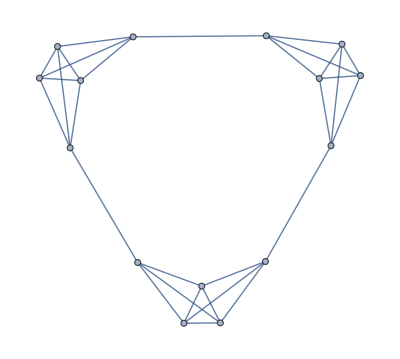

```mathematica
G[2,4]
```

```mathematica
Spectrum[%]
```

{{Root-2.20Root[5-7 #1-2 #1^2+#1^3&,1]-2.2044015503294316,2},{-1,8},{Root0.636Root[5-7 #1-2 #1^2+#1^3&,2]0.6355519407979247,2},{Root3.57Root[5-7 #1-2 #1^2+#1^3&,3]3.5688496095315068,2},{4,1}}

Z_10 for σ = 3.

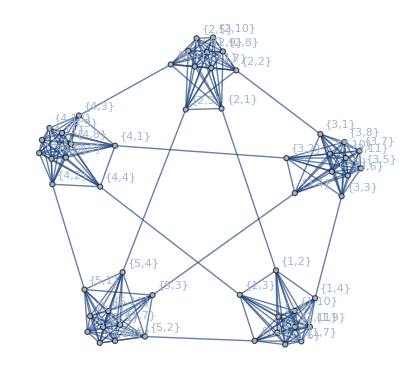

```mathematica
G[3,10,VertexLabels->Automatic]
```

```mathematica
Spectrum[%]
```

{{Root-2.67Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,1]-2.673406618914421,4},{Root-1.94Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,2]-1.9371580400262038,4},{-1,34},{Root0.113Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,3]0.11282166160568745,4},{Root0.891Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,4]0.8907593482328576,4},{Root9.61Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,5]9.60698364910208,4},{10,1}}

Vertex Partition and Quotient Matrix

```mathematica
Join[Table[{i,j},{i,5},{j,5,11}],List/@Flatten[Table[{i,j},{i,5},{j,4}],1]]
```

{{{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11}},{{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11}},{{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11}},{{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11}},{{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11}},{{1,1}},{{1,2}},{{1,3}},{{1,4}},{{2,1}},{{2,2}},{{2,3}},{{2,4}},{{3,1}},{{3,2}},{{3,3}},{{3,4}},{{4,1}},{{4,2}},{{4,3}},{{4,4}},{{5,1}},{{5,2}},{{5,3}},{{5,4}}}

```mathematica
QuotientAdjacencyMatrix[G[3,10],%]//MatrixForm
```

(6 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
7 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0)

```mathematica
Spectrum[%]
```

{{Root-2.67Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,1]-2.673406618914421,4},{Root-1.94Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,2]-1.9371580400262038,4},{-1,4},{Root0.113Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,3]0.11282166160568745,4},{Root0.891Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,4]0.8907593482328576,4},{Root9.61Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,5]9.60698364910208,4},{10,1}}

A_8 for σ = 4.

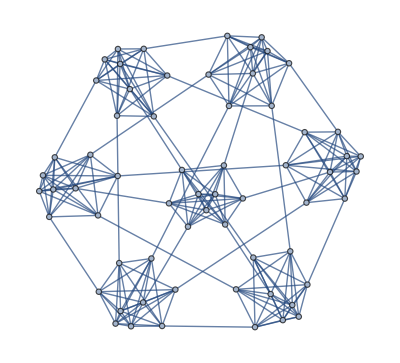

```mathematica
G[4,8]
```

```mathematica
Spectrum[%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

### Testing

```mathematica
G[2,4]
```

{{1,3}<->{1,4},{1,3}<->{1,5},{1,4}<->{1,5},{2,3}<->{2,4},{2,3}<->{2,5},{2,4}<->{2,5},{3,3}<->{3,4},{3,3}<->{3,5},{3,4}<->{3,5},{1,1}<->{1,3},{1,2}<->{1,3},{1,1}<->{1,4},{1,2}<->{1,4},{1,1}<->{1,5},{1,2}<->{1,5},{2,1}<->{2,3},{2,2}<->{2,3},{2,1}<->{2,4},{2,2}<->{2,4},{2,1}<->{2,5},{2,2}<->{2,5},{3,1}<->{3,3},{3,2}<->{3,3},{3,1}<->{3,4},{3,2}<->{3,4},{3,1}<->{3,5},{3,2}<->{3,5}}

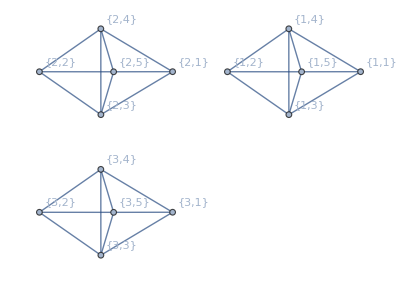

```mathematica
g=Graph[G[2,4],VertexLabels->Automatic]
```

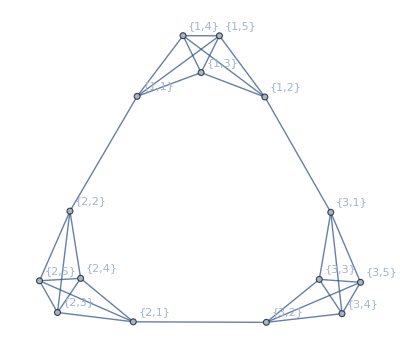

```mathematica
EdgeAdd[g,{{1,1}<->{2,2},{2,1}<->{3,2},{3,1}<->{1,2}}]
```

```mathematica
Spectrum[%30]
```

{{Root-2.20Root[5-7 #1-2 #1^2+#1^3&,1]-2.2044015503294316,2},{-1,8},{Root0.636Root[5-7 #1-2 #1^2+#1^3&,2]0.6355519407979247,2},{Root3.57Root[5-7 #1-2 #1^2+#1^3&,3]3.5688496095315068,2},{4,1}}

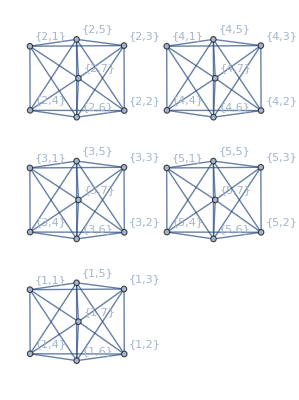

```mathematica
g=Graph[G[3,6],VertexLabels->Automatic]
```

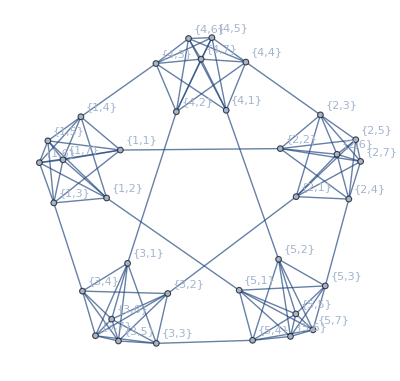

```mathematica
EdgeAdd[g,{{1,1}<->{2,2},{2,1}<->{3,2},{3,1}<->{4,2},{4,1}<->{5,2},{5,1}<->{1,2},
{1,3}<->{3,4},{3,3}<->{5,4},{5,3}<->{2,4},{2,3}<->{4,4},{4,3}<->{1,4}}]
```

```mathematica
VertexDegree[%]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
Spectrum[%33]
```

{{Root-2.61Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,1]-2.6100317386539094,4},{Root-1.74Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,2]-1.73763233450845,4},{-1,14},{Root0.0462Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,3]0.04621530258780768,4},{Root0.880Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,4]0.8800302144433776,4},{Root5.42Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,5]5.421418556131174,4},{6,1}}

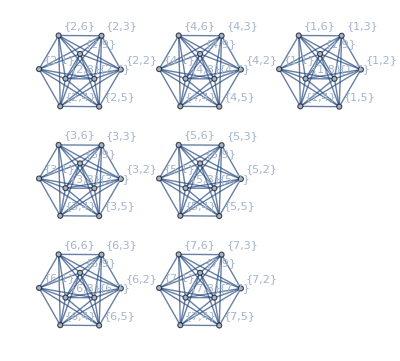

```mathematica
g=Graph[G[4,8],VertexLabels->Automatic]
```

```mathematica
{First[#],1}<->{Last[#],2}&/@Partition[Range[7],2,1,{1,1}]
```

{{1,1}<->{2,2},{2,1}<->{3,2},{3,1}<->{4,2},{4,1}<->{5,2},{5,1}<->{6,2},{6,1}<->{7,2},{7,1}<->{1,2}}

```mathematica
{First[#],3}<->{Last[#],4}&/@Partition[{1,3,5,2,7,4,6},2,1,{1,1}]
```

{{1,3}<->{3,4},{3,3}<->{5,4},{5,3}<->{2,4},{2,3}<->{7,4},{7,3}<->{4,4},{4,3}<->{6,4},{6,3}<->{1,4}}

```mathematica
{First[#],5}<->{Last[#],6}&/@Partition[{1,5,7,3,6,2,4},2,1,{1,1}]
```

{{1,5}<->{5,6},{5,5}<->{7,6},{7,5}<->{3,6},{3,5}<->{6,6},{6,5}<->{2,6},{2,5}<->{4,6},{4,5}<->{1,6}}

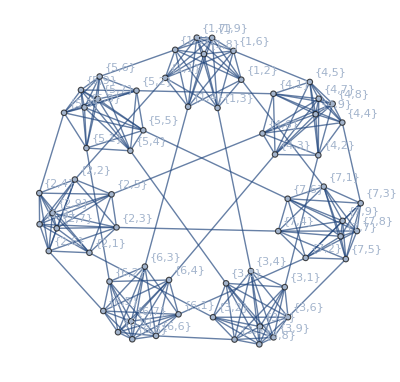

```mathematica
EdgeAdd[g,Join[%,%%,%%%]]
```

```mathematica
VertexDegree[%]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Spectrum[%%]
```

{{Root-2.95Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.945726548275878,1},{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,3},{Root-2.63Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.631026801505424,2},{Root-2.42Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.418377875757821,2},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,3},{Root-1.96Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-1.9558149132859004,1},{Root-1.60Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.6022728522004022,1},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,3},{Root-1.50Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.4984738367168853,2},{-1,20},{Root-0.275Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.2746426095317641,2},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,3},{Root-0.164Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.16391511063165878,1},{Root0.379Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.37931920563882626,1},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,3},{Root0.556Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.5560737985012758,2},{Root0.937Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9369758420490687,2},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,3},{Root0.950Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9496330226645139,1},{Root7.33Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.329471482961551,2},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,3},{Root7.34Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.3387771960905,1},{8,1}}

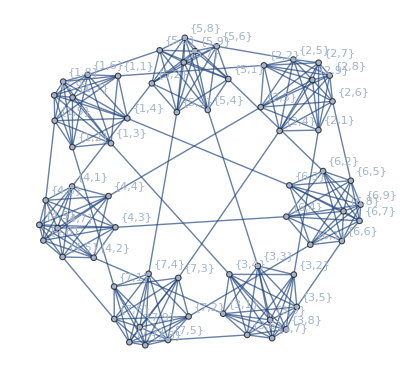

```mathematica
EdgeAdd[g,Join[
{First[#],1}<->{Last[#],2}&/@Partition[Range[7],2,1,{1,1}],
{First[#],3}<->{Last[#],4}&/@Partition[{1,3,5,7,2,4,6},2,1,{1,1}],
{First[#],5}<->{Last[#],6}&/@Partition[{1,4,7,3,6,2,5},2,1,{1,1}]
]]
```

```mathematica
VertexDegree[%]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Spectrum[%%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

```mathematica
Flatten[Table[{{i,1}<->{Mod[i-1,7,1],2},{i,3}<->{Mod[i-2,7,1],4},{i,5}<->{Mod[i-3,7,1],6}},{i,7}],1]
```

{{1,1}<->{7,2},{1,3}<->{6,4},{1,5}<->{5,6},{2,1}<->{1,2},{2,3}<->{7,4},{2,5}<->{6,6},{3,1}<->{2,2},{3,3}<->{1,4},{3,5}<->{7,6},{4,1}<->{3,2},{4,3}<->{2,4},{4,5}<->{1,6},{5,1}<->{4,2},{5,3}<->{3,4},{5,5}<->{2,6},{6,1}<->{5,2},{6,3}<->{4,4},{6,5}<->{3,6},{7,1}<->{6,2},{7,3}<->{5,4},{7,5}<->{4,6}}

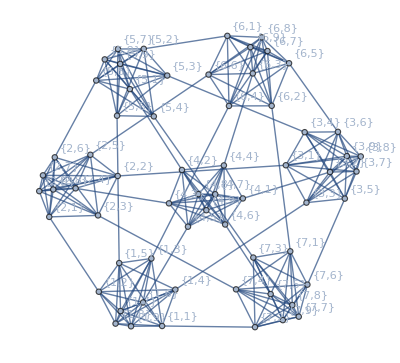

```mathematica
EdgeAdd[g,%96]
```

```mathematica
VertexDegree[%]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Spectrum[%%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

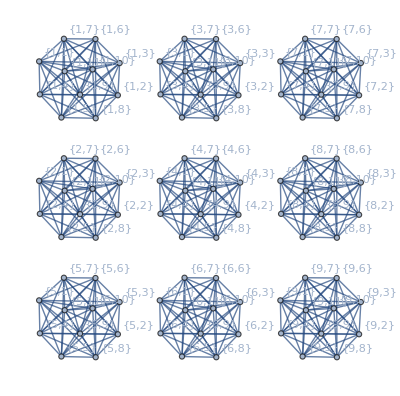

```mathematica
g=Graph[G[5,10],VertexLabels->Automatic]
```

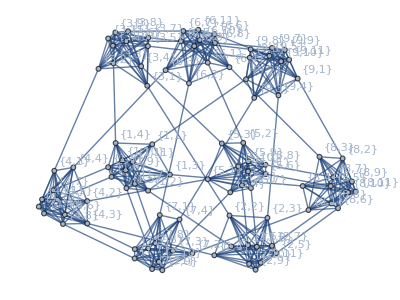

```mathematica
EdgeAdd[g,Flatten[Table[{{i,1}<->{Mod[i-1,9,1],2},{i,3}<->{Mod[i-2,9,1],4},{i,5}<->{Mod[i-3,9,1],6},{i,7}<->{Mod[i-3,9,1],8}},{i,9}],1]]
```

```mathematica
VertexDegree[%]
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
Spectrum[%%]
```

{{Root-2.90Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,1]-2.89842911796781,2},{Root-2.90Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,2]-2.8956519499770192,2},{-1-√3,8},{Root-2.47Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,3]-2.4693707245399286,2},{Root-2.42Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,4]-2.419883898654676,2},{Root-2.20Root[14-16 #1-8 #1^2+#1^3&,1]-2.19500700315004,2},{Root-2.07Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,5]-2.0662070620542234,2},{Root-1.95Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,6]-1.954593646794124,2},{Root-1.55Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,7]-1.549038172984497,2},{Root-1.41Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,8]-1.4114563475097823,2},{Root-1.40Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,9]-1.4015621037698829,2},{-1,34},{Root-0.411Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,10]-0.4114586910603308,2},{Root-0.407Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,11]-0.4068229274573423,2},{Root0.186Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,12]0.18611639723015846,2},{Root0.212Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,13]0.2117845057534735,2},{Root0.659Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,14]0.6587460638194268,2},{Root0.663Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,15]0.6633807492642345,2},{Root0.670Root[14-16 #1-8 #1^2+#1^3&,2]0.6695886221434443,2},{Root0.674Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,16]0.6737686615475472,2},{-1+√3,8},{Root0.966Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,17]0.966002130241794,2},{Root0.966Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,18]0.9660111086650132,2},{Root9.05Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,19]9.051842934447578,2},{Root9.16Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,20]9.155390092937147,2},{Root9.35Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,21]9.351431998863246,2},{Root9.53Root[14-16 #1-8 #1^2+#1^3&,3]9.525418381006595,2},{10,1}}

```mathematica
QuotientAdjacencyMatrix[g_Graph,s_List]:=SparseArray@Flatten[If[#1==#2,{#1,#2}->(2#3)/Length[s⟦#1⟧],{{#1,#2}->#3/Length[s⟦#1⟧],{#2,#1}->#3/Length[s⟦#2⟧]}]&@@@({First[#1],Last[#1],#2}&@@@Tally[EdgeList[g]/.Flatten[Thread/@MapIndexed[Rule[#1,First[#2]]&,s],1]]),1]
```

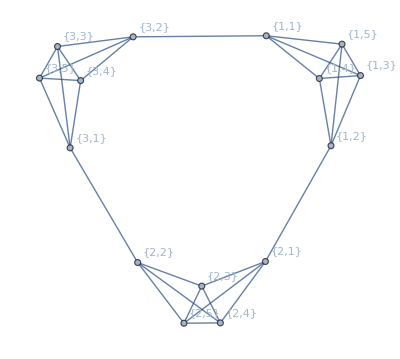

```mathematica
G[2,4,VertexLabels->Automatic]
```

```mathematica
Join[{{#,3},{#,4},{#,5}}&/@Range[3],{{#,1}}&/@Range[3],{{#,2}}&/@Range[3]]
```

{{{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}},{{3,3},{3,4},{3,5}},{{1,1}},{{2,1}},{{3,1}},{{1,2}},{{2,2}},{{3,2}}}

```mathematica
QuotientAdjacencyMatrix[G[2,4],Join[{{#,3},{#,4},{#,5}}&/@Range[3],{{#,1}}&/@Range[3],{{#,2}}&/@Range[3]]]//MatrixForm
```

(2 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 2 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 1
3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 1 | 0
3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0)